```mathematica
Needs["OpenCLLink`"]

FetchData[filename_]:=  Import[NotebookDirectory[]<>"../data/simulation/"<>filename];
ExportData[filename_, data_]:= Export[NotebookDirectory[]<>"../data/simulation/"<>filename, data];
```

## TEST

```mathematica
{width,height}={256,256};
jset=OpenCLMemoryAllocate[_Integer,{height,width}];
MCalc=OpenCLFunctionLoad[
File[NotebookDirectory[]<>"sim.cl"],
"mandelbrot",
{
{_Integer,_,"Output"},
_Integer,
_Integer,
_Integer
},{16,16},"Defines"->{"MAX_ITERATIONS"->8},
"ShellOutputFunction"->Print
];
```

(): Warning: Function mandelbrot is a kernel, so overriding noinline attribute. The function may be inlined when called.

```mathematica
Manipulate[
MCalc[jset,width,height, depth];
ReliefPlot[
OpenCLMemoryGet[jset],
ImageSize->256,
ColorFunction->"SunsetColors",
PerformanceGoal->"Quality"
],
{depth,10,256, 1}
]
```

OpenCLMemoryGet::gethdfld: OpenCLLink was not able to get memory handle with head Symbol, required head is OpenCLMemory.

ReliefPlot::input: Argument OpenCLMemoryGet[jset] at position 1 is not a 2 x 2 or larger numerical matrix of real values.

## Single update simulation

```mathematica
(*On[Assert]*)

ClearAll["Pop"];
SetAttributes[Pop,HoldFirst];
Pop[list_]:=With[{item=list[[1]]},list=Delete[list,1];item];

ClearAll["SimulateSingle"];
SimulateSingle[rateMatrix_, nodeThresholds_, startingAgentPositions_, maxSteps_] := Module[{MoveAgents, AreThereFailures , ComputeAvalancheSize, i, nNodes, nAgents, carCountsByNode, agentPositions, possibleAgentPositions, failedNodes},
nNodes = Length[rateMatrix];
If[nNodes != Length[nodeThresholds], Return[$Failed]];

possibleAgentPositions = Table[i, {i, 1, nNodes}];
nAgents = Length[agentPositions];
agentPositions = startingAgentPositions;	

MoveAgents[] := Module[{},
agentPositions = (
Assert[Total[rateMatrix[[;;, #]]] == 1];
RandomChoice[rateMatrix[[;;, #]]->possibleAgentPositions ]
) &/@ agentPositions;
];

AreThereFailures[] := Module[{},
carCountsByNode = Count[agentPositions, #] &/@ Table[i, {i, 1, nNodes}];
failedNodes = Append[(Transpose@Position[# < 0 &/@ (nodeThresholds -carCountsByNode ), True]), {}][[1]];

If[Length[failedNodes]>0, Return[True]];
False
];

ComputeAvalancheSize[node_] := Module[{avalancheSize, carCount, avalancheCarCounts, adjacentNodes, nodesToCheck, lockedNodes, currentNode, newNode, transitionProbabilities},
nodesToCheck = {node};
lockedNodes = {};
avalancheCarCounts = carCountsByNode;


While[Length@nodesToCheck >0,
currentNode = Pop[nodesToCheck];
Assert[avalancheCarCounts[[currentNode]] >0, "carCount"];

If[nodeThresholds[[currentNode]] -avalancheCarCounts[[currentNode]] >=0, Continue[]];

AppendTo[lockedNodes, currentNode];

If[Length@lockedNodes == nNodes, Break[]];

transitionProbabilities = Normal@rateMatrix[[currentNode]];
(transitionProbabilities[[#]] = 0 )&/@ lockedNodes;

(* If there is nowhere to go, we just lock this node and no transfer*)
If[Total@transitionProbabilities == 0,
Continue[];
];

transitionProbabilities /= Total[transitionProbabilities];

For[carCount = avalancheCarCounts[[currentNode]], carCount >0, carCount--,
Assert[nNodes == Length@transitionProbabilities, "nNodes"];

newNode = RandomChoice[transitionProbabilities->Table[x, {x, 1, nNodes}]];

Assert[newNode != currentNode, "currentNode"];
Assert[!MemberQ[lockedNodes, newNode], "lockedNodes"];
If[!MemberQ[nodesToCheck, newNode], AppendTo[nodesToCheck, newNode]];

avalancheCarCounts[[newNode]]++;
avalancheCarCounts[[currentNode]]--;
];
];

Assert[Total[avalancheCarCounts] == Total[carCountsByNode]];

Return[{node,Length@lockedNodes}];
];

For[i=1, i<=maxSteps,  i++, 
MoveAgents[];

If[!AreThereFailures[], Continue[]];
Break[];
];

If[Length@failedNodes == 0, Return[{}]];

Map[ComputeAvalancheSize, failedNodes]
];
```

## Generate agents

```mathematica
ClearAll["GenerateAgentsUniform"];
GenerateAgentsUniform[nAgents_,nNodes_]:=Table[RandomInteger[{1,nNodes}],nAgents];

ClearAll["GenerateOccupanciesUniform"];
GenerateOccupanciesUniform[nAgents_,nNodes_]:=Module[{occupancies},
occupancies = Table[0, nNodes];

Do[occupancies[[RandomInteger[{1, nNodes}]]]++, nAgents];

occupancies
];
```

## Simulation Code

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];
s = GenerateAgentsUniform[1000, VertexCount@g];
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

t = 20;
sampleCount = 30;
```

VertexCount::graph: A graph object is expected at position 1 in VertexCount[FetchData[g.mx]].

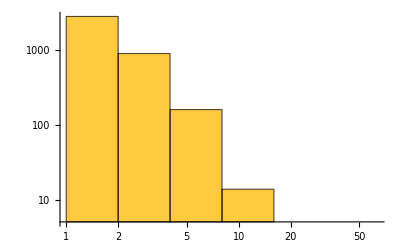

```mathematica
(*;;,;;,2 Selects avalanche size,;;,;;,1 selects start node*)
avalancheSizes=Flatten[ParallelTable[SimulateSingle[w,c,s,t][[;;, 2]],sampleCount]];
Histogram[avalancheSizes,{PowerRange[1, 100, 2]},  ScalingFunctions->{"Log", "Log"}, PlotRange->Full ]
```

```mathematica
VertexDegree@g // Sort
```

## Prepare data for CUDA

```mathematica
$DefaultParallelKernels = 8;
CloseKernels[];
LaunchKernels[];
```

```mathematica
ClearAll["ComputeCumRatesAndLinks"];
ComputeCumRatesAndLinks[g_, w_, arrayStart_:0] := Module[{maxLinks, nodeCount,lists},
maxLinks = Max@VertexDegree@g;
nodeCount = Length@w;

On[Assert];
lists = ParallelTable[Module[{col, cumulativeRate, nodeRates, nodeLinks, i, rate},
col = Normal@w[[j]];

Assert[Total@col == 1];

cumulativeRate = 0;
nodeRates = {};
nodeLinks = {};

(*Compute cumulative rates so random choice doesn't have to loop through the whole matrix*)
Assert[Length@col == nodeCount];
For[i = 1, i <= nodeCount, i++,
rate = col[[i]];
If[rate == 0, Continue[]];

cumulativeRate += rate;
AppendTo[nodeRates, cumulativeRate];
AppendTo[nodeLinks, i-(1-arrayStart)]; (* C++ counts from zero. Mathematica from 1.*)
];


Assert[Max@nodeRates == 1];
Assert[Length@nodeRates <= maxLinks];
Assert[Length@nodeLinks <= maxLinks];
Assert[Length@nodeRates == Length@nodeLinks];

(*Since array has to be square, we fill it with invalid values*)
While[Length@nodeRates < maxLinks,
AppendTo[nodeRates, -1];
AppendTo[nodeLinks, -1];
];

{nodeRates, nodeLinks}
], {j, 1, nodeCount}];

Return[Transpose@lists];
];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-naive.csv", rateList];
ExportData["link-list.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-speed.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-speed.csv", rateList];
ExportData["link-list-speed.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-morning.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-time.csv", rateList];
ExportData["link-list-time-morning.csv", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-evening.mx"];

result = ComputeCumRatesAndLinks[g, w];

rateList = result[[1]];
linkList = result[[2]];

rateList =Map[N, rateList, {2}];
ExportData["cumulative-rates-time.csv", rateList];
ExportData["link-list-time-evening.csv", linkList];
```

```mathematica
c= FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

ExportData["thresholds.csv", c];
ExportData["flows.csv", f];
```

## Multiple node sim

```mathematica
ClearAll["SimulateMulti"];
SimulateMulti[cumulativeRates_, linkList_, nodeThresholds_, nodeFlows_,  startingOccupancies_, maxSteps_] := 
Module[{nNodes, startingCarCount, ExecuteNode, nodeOccupancies},
nNodes = Length[cumulativeRates];
If[nNodes != Length[nodeThresholds], Return[$Failed]];
If[nNodes != Length[nodeFlows], Return[$Failed]];

startingCarCount = Total@startingOccupancies;

nodeOccupancies = {startingOccupancies};

ExecuteNode [nodeId_, t_] := Module[{maxCarsToMove, carsInNode, carsToMove, choices, links},
maxCarsToMove = nodeFlows[[nodeId]];
carsInNode = nodeOccupancies[[t, nodeId]];
choices = cumulativeRates[[nodeId]];
links = linkList[[nodeId]];

carsToMove = Floor@Min[{carsInNode, maxCarsToMove}];

(*ParallelDo here slows down by a lot due to memory overhead sigh*)
Do[
Module[{choice, linkId, destNode},
choice = RandomReal[];
linkId =SelectFirst[choices,choice <= #& -> "Index", -1];
Assert[linkId != -1];
destNode = links[[linkId]];

If[nodeThresholds[[destNode]] >= nodeOccupancies[[t, destNode]], 
nodeOccupancies[[t+1, destNode]]++;
nodeOccupancies[[t+1, nodeId]]--;
];
], carsToMove];
];

For[t=1, t<=maxSteps,  t++,
AppendTo[nodeOccupancies, nodeOccupancies[[-1]]];
Do[ExecuteNode[i, t], {i, 1, nNodes}];

Assert[Total[nodeOccupancies[t] == startingCarCount]];
];

nodeOccupancies
];
```

```mathematica
SimulateMulti[{{1}, {1}, {1}, {1}}, {{2, 3}, {3}, {4}, {1}}, {5, 1, 5, 5}, {2, 2, 2, 2},  {2, 0, 0, 2}, 10]
```

{{2,0,0,2},{2,2,0,0},{2,0,2,0},{0,2,0,2},{2,0,2,0},{0,2,0,2},{2,0,2,0},{0,2,0,2},{2,0,2,0},{0,2,0,2},{2,0,2,0}}

## Results

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-speed.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-speed.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-morning.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-time-morning.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-time-evening.mx"];

{rateList, linkList} = ComputeCumRatesAndLinks[g, w, 1];

ExportData["rate-list-time-evening.mx", rateList];
ExportData["link-list.mx", linkList];
```

```mathematica
{rateList, linkList} = {FetchData["rate-list-speed.mx"], FetchData["link-list.mx"]};(*ComputeCumRatesAndLinks[g, w, 1];*)
s = GenerateOccupanciesUniform[20000, Length@linkList];
c = 2 FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

t = 50;
sampleCount = 20;
```

```mathematica
result = ParallelTable[SimulateMulti[rateList, linkList, c, f, s, t], sampleCount, Method->"FinestGrained"];
```

```mathematica
Total @s
```

19874

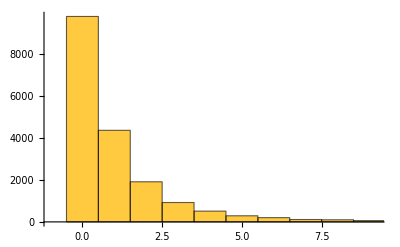

```mathematica
Histogram[[[1, -1]], {1}]
```

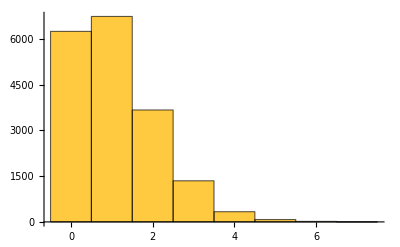

```mathematica
Histogram[[[1, 1]], {1}]
```

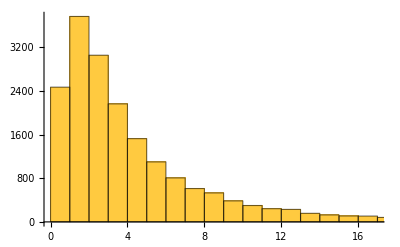

```mathematica
Histogram[c, {1}]
```

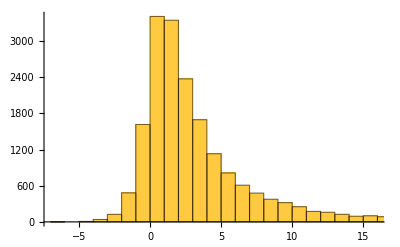

```mathematica
Histogram[(Floor/@c) - [[1, -1]]]
```

```mathematica
rateList
```